# Chapter 5

## Setup

```mathematica
Unprotect[DivisorSigma];

DivisorSigma[m_Integer]:=DivisorSigma[1,m];
SyntaxInformation[DivisorSigma]={"ArgumentsPattern"->{_,_.}};
Format[HoldPattern[DivisorSigma[m_]],TraditionalForm]:=
σ[m];

Protect[DivisorSigma];
```

```mathematica
Attributes[DivisorTau]=Listable;

DivisorTau[n_Integer]:=
DivisorSigma[0,n];

Format[DivisorTau,TraditionalForm]=τ;
```

```mathematica
PerfectNumberQ[n_]:=
DivisorSigma[n]===2*n;
```

```mathematica
ClearAll[MersenneExponent];
MersenneExponent[1]=2;
MersenneExponent[n_Integer?Positive]:=MersenneExponent[n]=
Module[{p=NextPrime[MersenneExponent[n-1]]},
While[!PrimeQ[2^p-1],
p=NextPrime[p]];
p];

ClearAll[MersennePrime];
MersennePrime[n_Integer?Positive]:=MersennePrime[n]=2^MersenneExponent[n]-1;

Attributes[MersennePrime]=Listable;
```

```mathematica
PrimesTo[x_?Positive]:=Prime@Range@PrimePi@x;
PrimesTo[x_?NumericQ]/;Im[x]==0={};
```

## Section 5.1

```mathematica
ClearAll[w];
w[x_?NumericQ]/;x∈Reals:=Times@@(1-1/PrimesTo[x]);
```

```mathematica
(1-1/PrimesTo[17.2])
```

{1/2,2/3,4/5,6/7,10/11,12/13,16/17}

```mathematica
{N[w[17.2]],1/Log[17.2]}
```

{0.180525,0.351505}

```mathematica
N[Times@@(1-1/PrimesTo[Sqrt[17.2]])]
```

0.333333

```mathematica
{Times@@(1-1/PrimesTo[Sqrt[50]]),1/Log[50]}//N
```

{0.228571,0.255622}

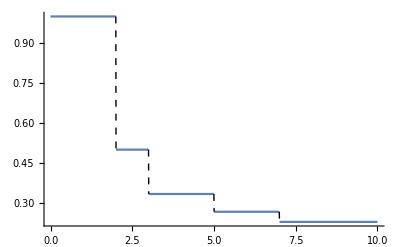

```mathematica
Plot[w[x],{x,0,10},PlotRange->All,
Exclusions->Map[x==#&,PrimesTo[10]],
ExclusionsStyle->Dashed
]
```

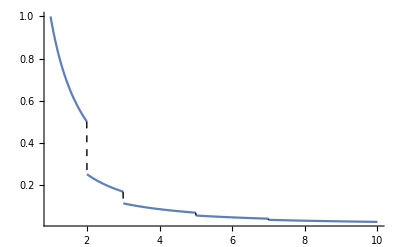

```mathematica
Plot[w[x]/x,{x,1,10},PlotRange->All,
Exclusions->Map[x==#&,PrimesTo[10]],
ExclusionsStyle->Dashed,
AxesOrigin->{0,0}
]
```

```mathematica
D[Log[𝓌[x]],x]==-𝓌[x]/x
```

𝓌'[x]/𝓌[x]==-𝓌[x]/x

```mathematica
DSolve[D[Log[𝓌[x]],x]==-𝓌[x]/x,𝓌,x]
```

{{𝓌→Function[{x},1/(-C[1]+Log[x])]}}

### Exercise 5.1.1

```mathematica
BeginPackage["Exercise511`",{"Global`"}];
```

```mathematica
random[]:=random[1];
random[n_Integer?NonNegative]:=RandomInteger[{9500,10400},{n}];
```

```mathematica
?PrimePi
```

PrimePi[x] gives the number of primes π(x) less than or equal to x.

```mathematica
countPrimesBetween[x_,x_]=0;
countPrimesBetween[m_,n_]/;m<n:=PrimePi[n]-PrimePi[m];
countPrimesBetween[m_,n_]/;n≤m=0;
```

```mathematica
countPrimesBetween[#,#+100]&[0]
```

25

```mathematica
Prime[25]
```

97

```mathematica
data=countPrimesBetween[#,#+100]&/@random[1000];
```

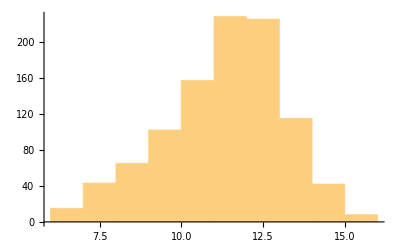

```mathematica
Histogram[data]
```

```mathematica
N[Mean[data]/100]
```

0.1081

```mathematica
1.0/Log[10000]
```

0.108574

```mathematica
EndPackage[];
Remove["Exercise511`*"]
```

### Exercise 5.1.2

Not independent.

### Text

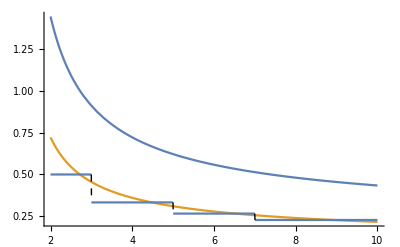

```mathematica
Show[
Plot[{1/Log[x],1/(2*Log[x])},{x,2,10},PlotRange->{0,All},AxesOrigin->{0,0}],
Plot[w[x],{x,2,10},PlotRange->All,
Exclusions->Map[x==#&,PrimesTo[10]],
ExclusionsStyle->Dashed
]
]
```

### Exercise 5.1.3

```mathematica
BeginPackage["Exercise513`",{"Global`"}];
```

```mathematica
bounds={NextPrime[10000,-60],NextPrime[10000,60]}
```

{9439,10559}

```mathematica
primes=Prime[Range@@PrimePi[bounds]];
```

```mathematica
Labeled[Framed[Multicolumn[primes,10]],Style[StringForm["Primes near ``",NumberForm[10000,DigitBlock->3,NumberSeparator->" "]],"Text"],Top]
```

9439 | 9547 | 9677 | 9781 | 9871 | 10007 | 10111 | 10223 | 10321 | 10453
9461 | 9551 | 9679 | 9787 | 9883 | 10009 | 10133 | 10243 | 10331 | 10457
9463 | 9587 | 9689 | 9791 | 9887 | 10037 | 10139 | 10247 | 10333 | 10459
9467 | 9601 | 9697 | 9803 | 9901 | 10039 | 10141 | 10253 | 10337 | 10463
9473 | 9613 | 9719 | 9811 | 9907 | 10061 | 10151 | 10259 | 10343 | 10477
9479 | 9619 | 9721 | 9817 | 9923 | 10067 | 10159 | 10267 | 10357 | 10487
9491 | 9623 | 9733 | 9829 | 9929 | 10069 | 10163 | 10271 | 10369 | 10499
9497 | 9629 | 9739 | 9833 | 9931 | 10079 | 10169 | 10273 | 10391 | 10501
9511 | 9631 | 9743 | 9839 | 9941 | 10091 | 10177 | 10289 | 10399 | 10513
9521 | 9643 | 9749 | 9851 | 9949 | 10093 | 10181 | 10301 | 10427 | 10529
9533 | 9649 | 9767 | 9857 | 9967 | 10099 | 10193 | 10303 | 10429 | 10531
9539 | 9661 | 9769 | 9859 | 9973 | 10103 | 10211 | 10313 | 10433 | 10559Primes near 10 000

```mathematica
PrimePi[9500]
```

1177

```mathematica
PrimePi[9500]+Length@Select[primes,9500<#≤9600&]
```

1184

```mathematica
PrimePi[9600]
```

1184

```mathematica
EndPackage[];
```

### Text

```mathematica
Integrate[1/Log[x],x]
```

LogIntegral[x]

```mathematica
TraditionalForm@%
```

x

```mathematica
?PrimeOmega
```

PrimeOmega[n] gives the number of prime factors counting multiplicities Ω(n) in n.

```mathematica
ClearAll[ω,ns]
```

```mathematica
ω[n_Integer]:=Boole@PrimeQ[n]
```

```mathematica
ns=5*10^Range[3]
```

{50,500,5000}

```mathematica
PrimePi[ns]
```

{15,95,669}

```mathematica
N[LogIntegral[ns]]
```

{18.4687,101.794,684.281}

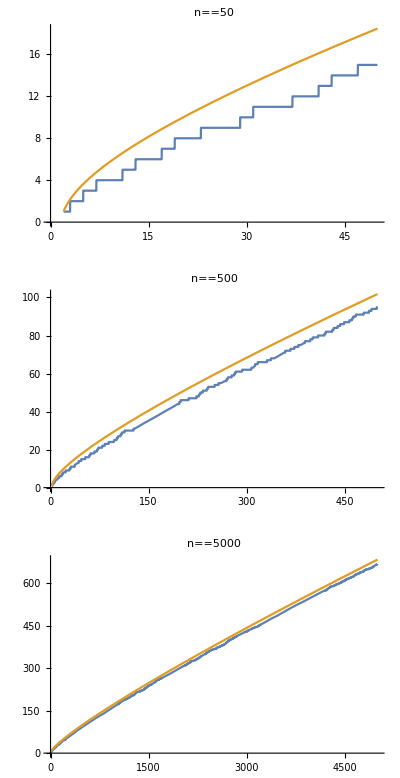

```mathematica
GraphicsColumn[
Plot[{PrimePi[x],LogIntegral[x]},{x,2,#},AxesOrigin->{0,0},PlotLabel->(HoldForm[n==#])]&/@ns,

ImageSize->400
]
```

### Exercise 5.1.4

```mathematica
TableForm[
Array[With[{x:=10^#},
{HoldForm[x],PrimePi[x],LogIntegral[x]//N,
x/Log[x]//N,
PrimePi[x]/LogIntegral[x]//N,
PrimePi[x]/(x/Log[x])//N
}]&,
8,2],

TableHeadings->{None,TraditionalForm/@{x,PrimePi[x],LogIntegral[x],x/Log[x],PrimePi[x]/LogIntegral[x],PrimePi[x]/HoldForm[x/Log[x]]}}
]
```

x | x | x | x/(log(x)) | x/x | x/(x/(log(x)))
10^2 | 25 | 30.1261 | 21.7147 | 0.829844 | 1.15129
10^3 | 168 | 177.61 | 144.765 | 0.945895 | 1.1605
10^4 | 1229 | 1246.14 | 1085.74 | 0.986248 | 1.13195
10^5 | 9592 | 9629.81 | 8685.89 | 0.996074 | 1.10432
10^6 | 78498 | 78627.5 | 72382.4 | 0.998352 | 1.08449
10^7 | 664579 | 664918. | 620421. | 0.99949 | 1.07117
10^8 | 5761455 | 5.76221×10^6 | 5.42868×10^6 | 0.999869 | 1.0613
10^9 | 50847534 | 5.08492×10^7 | 4.82549×10^7 | 0.999967 | 1.05373

### Text

```mathematica
Limit[Product[(1-1/Prime[k]),{k,1,x}]*Log[x],x->Infinity]
```

Limit[Log[x] ∏_(k=1)^x (1-1/Prime[k]),x→∞]

```mathematica
Exp[-EulerGamma]/Log[10000.]
```

0.0609597

```mathematica
Times@@(1-1/PrimesTo[10000])//N
```

0.0608847

```mathematica
Exp[-EulerGamma]/Log[1000.]
```

0.0812796

```mathematica
Times@@(1-1/PrimesTo[1000])//N
```

0.0809653

### Exercise 5.1.5

∏_(p ∈ ℙ
p < x) (1-1/p)∼(exp(-γ))/(log(x))

(exp(-ℽ))/(log(x))==1/(log(x^(exp(ℽ))))

```mathematica
PowerExpand[1/Log[x^Exp[EulerGamma]]]
```

ⅇ^-EulerGamma/Log[x]

∏_(p ∈ ℙ
p < x^(exp(-γ))) (1-1/p)∼1/(log(x))

## Section 5.2

```mathematica
With[{row={2^(2*n),(2n)!/(n!*n!)}},
TableForm[
Table[row,{n,1,6}],
TableHeadings->{Automatic,row}
]]
```

| 2^(2 n) | ((2 n)!)/(n!)^2
1 | 4 | 2
2 | 16 | 6
3 | 64 | 20
4 | 256 | 70
5 | 1024 | 252
6 | 4096 | 924

### Exercise 5.2.1

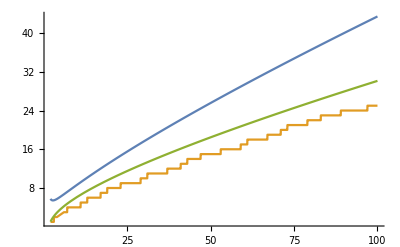

```mathematica
Plot[{2x/Log[x],PrimePi[x],LogIntegral[x]},{x,2,100},AxesOrigin->{0,0},PlotRange->{0,All}]
```

```mathematica
FindRoot[x-3.44*(Log[2]+x)/4,{x,1}]
```

{x→4.2579}

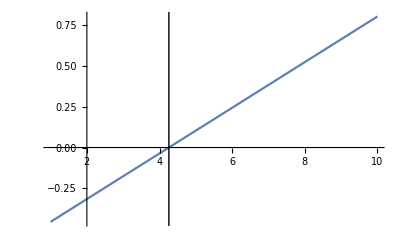
-Graphics-x_0==4.2579

```mathematica
With[{expr=x-3.44*(Log[2]+x)/4},
With[{x0=x/.FindRoot[x-3.44*(Log[2]+x)/4,{x,1}]},
Labeled[
Plot[expr,{x,1,10},
Epilog->(Line[{{x0,-5},{x0,5}}])],

Subscript[x, 0]==x0
]]]
```

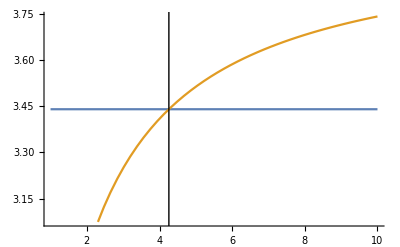
-Graphics-x_0==4.2579

```mathematica
With[{expr=x-3.44*(Log[2]+x)/4},
With[{x0=x/.FindRoot[x-3.44*(Log[2]+x)/4,{x,1}]},
Labeled[
Plot[{3.44,4x/(Log[2]+x)},{x,1,10},
Epilog->(Line[{{x0,-5},{x0,5}}])],

Subscript[x, 0]==x0
]]]
```

### Text

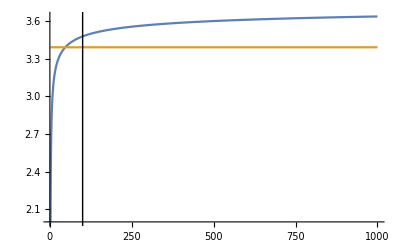

```mathematica
Plot[{4*Log[n]/Log[2n],3.39},{n,2,1000},PlotRange->All,
Epilog->Line[{{100,-10},{100,10}}]
]
```

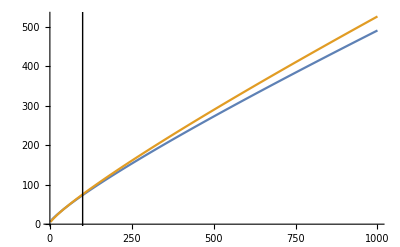

```mathematica
Plot[{3.39*n/Log[n],4*n/Log[2*n]},{n,2,1000},PlotRange->All,
Epilog->Line[{{100,-10},{100,1000}}]
]
```

```mathematica
Binomial[11,7]
```

330

```mathematica
PrimePi[11]
```

5

```mathematica
11^PrimePi[11]
```

161051

2^n==(1+1)^n==∑_(k=0)^n Binomial[n, k]≤(n+1) n^n

```mathematica
2^11
```

2048

```mathematica
compare[n_Integer?NonNegative]:=
{2^n,(n+1)*n^PrimePi[n]};
```

```mathematica
compare[11]
```

{2048,1932612}

```mathematica
compare[5]
```

{32,750}

```mathematica
PowerExpand[Log[2^n]]
```

n Log[2]

```mathematica
PowerExpand[Log[(n+1)*n^PrimePi[n]]]
```

Log[1+n]+Log[n] PrimePi[n]

```mathematica
Simplify@Quiet[Solve[2^n==(n+1)*n^ℼ,ℼ],Solve::ifun]
```

{{ℼ→-Log[2^-n (1+n)]/Log[n]}}

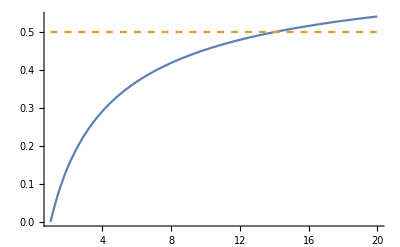

```mathematica
Plot[
{Log[2]-Log[n+1]/n,1/2},{n,1,20},AxesOrigin->{0,0},

PlotStyle->{Automatic,Dashed},

PlotRange->All]
```